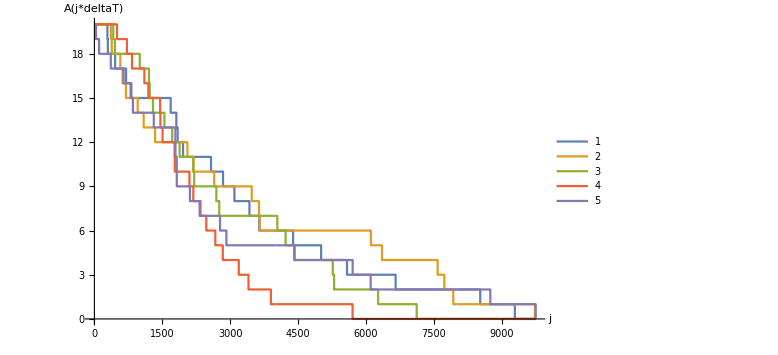

```mathematica
gillespie[k_,t0_,A0_]:=(
tList = {t0};
AList = {A0};
A=A0;
t=t0;
While[A>0,
rho = RandomVariate[UniformDistribution[{0,1}]];
alpha0 = A*k;
tau = -Log[rho]/alpha0;
A=A-1;
t=t+tau;
AppendTo[tList,t];
AppendTo[AList,A];
];

{tList,AList}
)

(*Parameters*)
t0=0;
A0=20;
tries =10;
k=0.1;

(*Get solutions*)
solList=Table[0,tries];
For[l=1,l≤tries,l++,
solList[[l]]=gillespie[k,t0,A0];
];

(*Find the minimum timestep and maximum stopping time*)
tauMin = 
Min[
Table[
Min[
Table[solList[[j]][[1]][[i+1]]-solList[[j]][[1]][[i]],{i,1,Length[solList[[j]][[1]]]-1}]
],{j,1,tries}]
];
TMax = Max[
Table[solList[[j]][[1]][[Length[solList[[j]][[1]]]]],{j,1,tries}]];
(*Find the delta*)
n=Ceiling[TMax/tauMin];
deltaT = TMax / n;

(*Create a list of values for the Al(j*deltaT) *)
moleculeCountTime = Table[Table[0,n],tries];
For[l=1,l≤tries,l++,
cIndex=1;
(*cIndex+1 in comparison, because we have a starting 0 in solList[[l]][[1]].Check if the index is at the size of the time list, then we don't have to increment it.*)
For[j=1,j≤n,j++,
If[cIndex!=Length[solList[[l]][[1]]],
If[j*deltaT>=solList[[l]][[1]][[cIndex+1]],
cIndex=cIndex+1];
];
moleculeCountTime[[l]][[j]]=solList[[l]][[2]][[cIndex]];
];
];


(*Plot*)
ListStepPlot[Table[moleculeCountTime[[l]],{l,1,tries}],PlotLegends->Table[j,{j,1,tries}],AxesLabel->{Style["j",16],Style["A(j*deltaT)",16]}, ImageSize->Large]
```